```mathematica
boxlength = 40;
σ=1;
Δx=0.08;
Δt=0.002;
tmax=3;
x0=-10;
barrierwidth=8;
k0=7;
V0=k0^2/2;
α=I Δt/(4(Δx)^2);
```

```mathematica
Unprotect[HeavisideTheta]
HeavisideTheta[0.]=1
Protect[HeavisideTheta]
```

{HeavisideTheta}

1

{HeavisideTheta}

```mathematica
psi[x_,0]=Exp[I k0 (x-x0)]Exp[-(x-x0)^2/(2σ^2)] ;
psilist={};
psi0=Table[{x,psi[x,0]},{x,-boxlength/2,boxlength/2,Δx}];
AppendTo[psilist,psi0];
V=Table[V0*HeavisideTheta[barrierwidth/2-x]*HeavisideTheta[x+barrierwidth/2],{x,-boxlength/2,boxlength/2,Δx}];
β=Table[I Δt/2(1/(Δx)^2+V[[i]]),{i,1,Length[V]}];
```

```mathematica
Length[psi0]
```

501

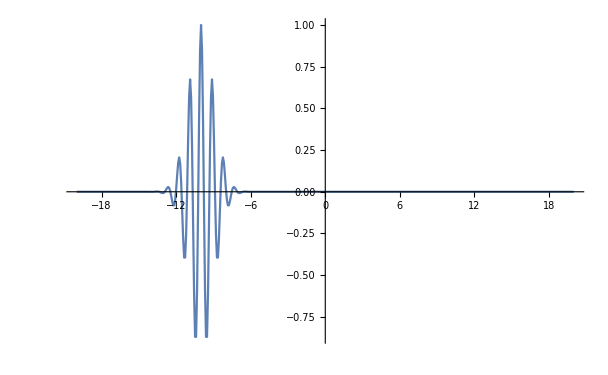

```mathematica
ListPlot[Re[psi0],PlotRange->All,Joined->True]
```

```mathematica
D1=Table[0,{i,1,boxlength/Δx+1},{j,1,boxlength/Δx+1}];
D2=Table[0,{i,1,boxlength/Δx+1},{j,1,boxlength/Δx+1}];
```

```mathematica
For[i=1,i≤boxlength/Δx+1,i++,If[i==1,D1[[i,i]]=1-β[[i]];D1[[i,i+1]]=α,If[i==Floor[boxlength/Δx+1],D1[[i,i-1]]=α;D1[[i,i]]=1-β[[i]],D1[[i,i-1]]=α;D1[[i,i]]=1-β[[i]];D1[[i,i+1]]=α]]]
For[i=1,i≤boxlength/Δx+1,i++,If[i==1,D2[[i,i]]=1+β[[i]];D2[[i,i+1]]=-α,If[i==Floor[boxlength/Δx+1],D2[[i,i-1]]=-α;D2[[i,i]]=1+β[[i]],D2[[i,i-1]]=-α;D2[[i,i]]=1+β[[i]];D2[[i,i+1]]=-α]]]
```

```mathematica
D2inv=Inverse[D2];
```

```mathematica
For[t=0,t≤tmax,t=t+Δt,AppendTo[psilist,Transpose[{Transpose[Last[psilist]][[1]],D2inv.D1.(Transpose[Last[psilist]][[2]])}]]]
```

```mathematica
Dimensions[psilist]
```

{1002,501,2}

```mathematica
cutpsilist=Re[psilist[[1;;-1;;20]]];
```

```mathematica
ListAnimate[Map[ListPlot[#,Joined->True,PlotRange->All]&,cutpsilist]]
```

```mathematica
psilist2=Map[Append[#,Arg[#[[2]]]]&,psilist,{2}];
psilist3=Map[MapThread[Append,{#,(RotateLeft[Last[Transpose[#]]]-RotateRight[Last[Transpose[#]]])/(2Δx)}]&,psilist2];
```

```mathematica
psilist2=Map[Append[#,ArcTan[Im[#[[2]]]/Re[#[[2]]]]]&,psilist,{2}];
psilist3=Map[MapThread[Append,{#,(RotateLeft[Last[Transpose[#]]]-Last[Transpose[#]])/Δx}]&,psilist2];
```

```mathematica
psilist3[[100]]//MatrixForm;
```

```mathematica
trajectories={};
AppendTo[trajectory,xinit];
For[xinit=-10,xinit≤-5,xinit+=1,trajectory={};AppendTo[trajectory,xinit];
For[ti=0,ti≤tmax,ti+=Δt,xloc=Last[trajectory];If[Abs[xloc]>boxlength/2,Break,velocity=SelectFirst[psilist3[[IntegerPart[ti/Δt+1]]],xloc-Δx/2<=#[[1]]≤xloc+Δx/2&][[4]];AppendTo[trajectory,Last[trajectory]+velocity*Δt]]];AppendTo[trajectories,trajectory]]
```

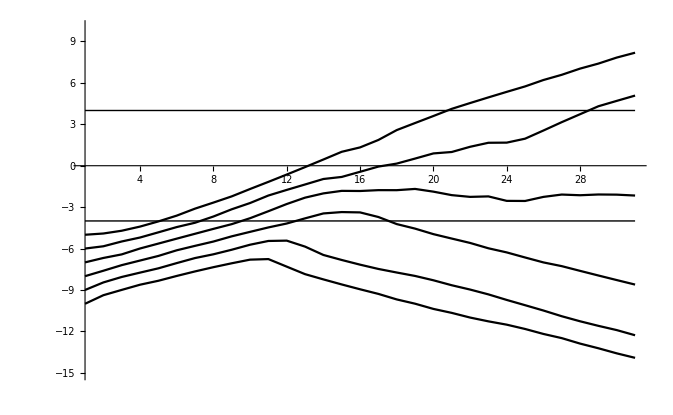

```mathematica
Show[ListLinePlot[trajectories[[All,1;;-1;;50]],PlotStyle->Black,PlotRange->{{1,31},{-15,10}}],Graphics[{Line[{{1,barrierwidth/2},{31,barrierwidth/2}}],Line[{{1,-barrierwidth/2},{31,-barrierwidth/2}}]}]]
```

```mathematica
psilist4=psilist3[[All,All,2]]
```

{{1.22151×10^-22-1.49264×10^-22 ⅈ,4.05486×10^-22-1.3661×10^-22 ⅈ,9.17234×10^-22+2.19645×10^-22 ⅈ,1.44655×10^-21+1.47471×10^-21 ⅈ,9.62442×10^-22+4.39131×10^-21 ⅈ,-3.28067×10^-21+9.15067×10^-21 ⅈ,490,4.74212×10^-192+2.08867×10^-192 ⅈ,2.69813×10^-193+3.97865×10^-193 ⅈ,1.59103×10^-195+4.42851×10^-194 ⅈ,-2.03113×10^-195+3.51405×10^-195 ⅈ,-3.26494×10^-196+1.7277×10^-196 ⅈ},1000,{1}}
 |  |  |  |

```mathematica
Dimensions[psilist4]
```

{1502,1001}

```mathematica
ListPlot3D[Re[psilist4[[;;;;10]]],PlotRange->All]
```

-Graphics3D-